```mathematica
n=300; m=10000;
```

```mathematica
(*En este codigo, se leen los datos exportados, se hace el grafo t, y la contraparte aleatoria r. Se analizan la distribucion de grados (comun a ambos), el numero de CCs y el tamaño de las mismas. Posteriormente se corrige el hecho de los nodos sin vecinos, al añadirle {1} por cada nodo faltante en las listas de CC, y agregarle un {0} en la lista de vertex degree. Posteriormente se exporta a 'lvd'  (list of vertex degree) la lista de valores que tiene la red para los grados de los nodos, lo mismo se hace para lncct 'list of number of Connected Components' y lscct 'list of sizes of connected components'. Se generan las contrapartes aleatorias y se analizan sus propiedades, diferenciandose de las redes de parentesco acá en que sus elementos terminan en -r en vez de -t por ejemplo lsccr, lnccr. *)
```

```mathematica
kaux={}; cc={}; ncct=0; nccr=0; x=0; lncct={}; lnccr={}; lvd={}; lscct={}; lsccr={};lgcct={}; lmcct={}; lassortt={}; lgccr={}; lmccr={}; lassortr={}; distt=ConstantArray[0,1000]; distr=ConstantArray[0, 1000]; diamt={}; diamr={}; llcct={};llccr={}; Do[kaux={};cc={}; x=0;  {spression=ToExpression[StringSplit[ReadLine["D:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 6 - Maestria 1\\Trabajo Especial\\Net_Generation\\N300\\n0500.txt"]]]; While[spression≠ {0,0}, {kaux=Join[kaux, {spression}], spression=ToExpression[StringSplit[ReadLine["D:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 6 - Maestria 1\\Trabajo Especial\\Net_Generation\\N300\\n0500.txt"]]]}],t=Table[kaux[[i,1]]<->kaux[[i,2]], {i, 1, Length[kaux]}], r=t, Do[{r1=RandomInteger[{1,Length[t] }], r2=RandomInteger[{1,Length[t] }], help=r[[r1, 2]], r[[r1, 2]]=r[[r2,2]], r[[r2, 2]]=help},n], v=VertexDegree[Graph[t]],cct=ConnectedComponents[Graph[t]],ccr=ConnectedComponents[Graph[r]],  x=Evaluate[n-Total[Table[Length[cct[[i]]], {i, 1, Length[cct]}]]], llcct=Join[llcct, LocalClusteringCoefficient[Graph[t]]],llccr=Join[llccr, LocalClusteringCoefficient[Graph[r]]], cct=ConnectedComponents[Graph[t]],ccr=ConnectedComponents[Graph[r]], lscct=Join[lscct, Table[Length[cct[[i]]], {i, 1, Length[cct]}]],lsccr=Join[lsccr, Table[Length[ccr[[i]]], {i, 1, Length[ccr]}]],Do[{ cct=Join[cct, {1}], v=Join[v, {0}], llcct=Join[llcct, {0}], lscct=Join[lscct, {0}]}, x],  x=Evaluate[n-Total[Table[Length[ccr[[i]]], {i, 1, Length[ccr]}]]],Do[{ ccr=Join[ccr, {1}], llccr=Join[llccr, {0}], lsccr=Join[lsccr, {0}]}, x], ncct=Length[cct], nccr=Length[ccr], lvd=Join[lvd, v],  lncct=Join[lncct, {ncct}] , lnccr=Join[lnccr, {nccr}],  lgcct=Join[lgcct, {GlobalClusteringCoefficient[Graph[t]]}], lgccr=Join[lgccr, {GlobalClusteringCoefficient[Graph[r]]}] , lmcct=Join[lmcct, {MeanClusteringCoefficient[Graph[t]]}], lmccr=Join[lmccr, {MeanClusteringCoefficient[Graph[r]]}] , lassortt=Join[lassortt, {GraphAssortativity[Graph[t]]}], lassortr=Join[lassortr, {GraphAssortativity[Graph[r]]}], f=DeleteCases[Flatten[UpperTriangularize[GraphDistanceMatrix[Subgraph[t, First[ConnectedComponents[t]]]]]], 0],  Do[{distt[[i]]=distt[[i]]+2*Count[f, i]}, {i, 1, 100}], diamt=Join[diamt, {Max[f]}], f=DeleteCases[Flatten[UpperTriangularize[GraphDistanceMatrix[Subgraph[r, First[ConnectedComponents[r]]]]]], 0], Do[{distr[[i]]=distr[[i]]+2*Count[f, i]}, {i, 1, 100}], diamr=Join[diamr, {Max[f]}]} , m];
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
(*Analisis de Vertex Degree*)
```

```mathematica
blvd=HistogramList[lvd]; hlvd=Table[{Floor[(blvd[[1, i]]+blvd[[1, i+1]])/2],blvd[[2, i]]/(Length[lvd]*(blvd[[1,2]]-blvd[[1,1]]))}, {i, 1, Length[blvd[[2]]]}]; TableForm[N[hlvd]]
```

```mathematica
Print[Mean[N[lvd]]]; Print[StandardDeviation[N[lvd]]];
```

1.79676

1.33731

```mathematica
(*Analisis de Number of Connected Components*)
```

```mathematica
blncct=HistogramList[lncct]; hlncct=Table[{Floor[(blncct[[1, i]]+blncct[[1, i+1]])/2],blncct[[2, i]]/(Length[lncct]*(blncct[[1,2]]-blncct[[1,1]]))}, {i, 1, Length[blncct[[2]]]}]; TableForm[N[hlncct]]
```

62. | 0.00014
67. | 0.00076
72. | 0.00468
77. | 0.01214
82. | 0.02608
87. | 0.0393
92. | 0.04386
97. | 0.03734
102. | 0.02168
107. | 0.0104
112. | 0.00274
117. | 0.00074
122. | 0.0001
127. | 0.00004

```mathematica
blnccr=HistogramList[lnccr]; hlnccr=Table[{Floor[(blnccr[[1, i]]+blnccr[[1, i+1]])/2],blnccr[[2, i]]/(Length[lnccr]*(blnccr[[1,2]]-blnccr[[1,1]]))}, {i, 1, Length[blnccr[[2]]]}]; TableForm[N[hlnccr]]
```

37. | 0.00004
42. | 0.00106
47. | 0.00502
52. | 0.01712
57. | 0.03654
62. | 0.04918
67. | 0.04542
72. | 0.02856
77. | 0.01172
82. | 0.0041
87. | 0.00108
92. | 0.0001
97. | 0.00006

```mathematica
Print[Mean[N[lncct]]]; Print[StandardDeviation[N[lncct]]]; Print[Mean[N[lnccr]]]; Print[StandardDeviation[N[lnccr]]];
```

91.3823

8.79241

63.7696

7.82342

```mathematica
(*Analisis de Size of Connected Components*)
```

```mathematica
w=(Max[lscct]-Min[lscct])/Sqrt[Length[lscct]]; blscct=HistogramList[lscct, {Min[lscct], Max[lscct], w}]; hlscct=Table[{Floor[blscct[[1, i]]], blscct[[2, i]]/(Length[lscct]*w)}, {i, 1, Length[blscct[[2]]]}];TableForm[N[hlscct]]
```

```mathematica
w=(Max[lsccr]-Min[lsccr])/Sqrt[Length[lsccr]]; blsccr=HistogramList[lsccr, {Min[lsccr], Max[lsccr], w}]; hlsccr=Table[{Floor[blsccr[[1, i]]], blsccr[[2, i]]/(Length[lsccr]*w)}, {i, 1, Length[blsccr[[2]]]}];TableForm[N[hlsccr]]
```

```mathematica
(*Analisis de Global and Mean Clusstering Coefficients*)
```

```mathematica
Print[Mean[N[lgcct]]];Print[ StandardDeviation[N[lgcct]]];Print[Mean[N[lgccr]]];Print[ StandardDeviation[N[lgccr]]]
```

0.442913

0.042909

0.00694267

0.00672125

```mathematica
Print[Mean[N[lmcct]]];Print[ StandardDeviation[N[lmcct]]];Print[Mean[N[lmccr]]];Print[ StandardDeviation[N[lmccr]]]
```

0.286783

0.0371119

0.0042937

0.0047927

```mathematica
(*Analisis de Assortativity*)
```

```mathematica
Print[Mean[N[lassortt]]];Print[ StandardDeviation[N[lassortt]]];Print[Mean[N[lassortr]]];Print[ StandardDeviation[N[lassortr]]]
```

0.413974

0.0858589

0.036948

0.0622501

```mathematica
(*Analisis de d en kinship*)
```

```mathematica
T=Total[distt]; M=N[Sum[{i*distt[[i]]}, {i, 1, Length[distt]}]/T];Print[M];SD=N[Sqrt[Sum[distt[[i]]*(i-M)^2, {i, 1, Length[distt]}]/(T-1)]]; Print[SD];
```

{9.32988}

{5.64602}

```mathematica
(*Analisis de d en random*)
```

```mathematica
T=Total[distr]; M=N[Sum[{i*distr[[i]]}, {i, 1, Length[distr]}]/T];Print[M];SD=N[Sqrt[Sum[distr[[i]]*(i-M)^2, {i, 1, Length[distr]}]/(T-1)]]; Print[SD];
```

{8.07446}

{3.31203}

```mathematica
(*Analisis de D en Kinship y random*)
```

```mathematica
Print[N[Mean[diamt]]];Print[N[StandardDeviation[diamt]]];Print[N[Mean[diamr]]];Print[N[StandardDeviation[diamr]]];
```

19.0559

6.21811

20.3109

3.61773

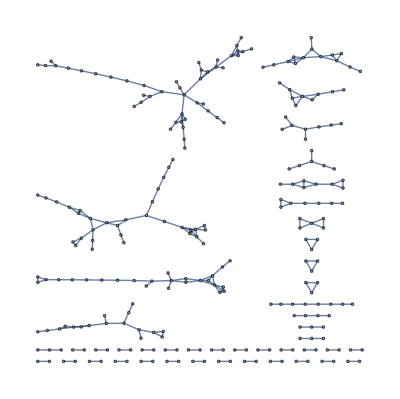

```mathematica
Graph[t]
```